```mathematica
ϕ=1/(1+Exp[-x/(Sqrt[2]ϵ)])
```

1/(1+ⅇ^(-x/(√2 ϵ)))

```mathematica
ψ=1/(1+Exp[x/(Sqrt[2]ϵ)])
```

1/(1+ⅇ^(x/(√2 ϵ)))

```mathematica
V = (1/4)ϕ^2(1-ϕ)^2
```

((1-1/(1+ⅇ^(-x/(√2 ϵ))))^2)/(4 (1+ⅇ^(-x/(√2 ϵ)))^2)

```mathematica
Integrate[V+ϵ^2(D[ϕ,x])^2/2,{x,-∞,∞}]
```

```mathematica
ConditionalExpression[ϵ/(6 √2), ]
hphi = ϕ^2(3-2ϕ)
```

ConditionalExpression[ϵ/(6 √2), ]

(3-2 ϕ) ϕ^2

```mathematica
hpsi = ψ^2(3-2ψ)
```

(3-2 ψ) ψ^2

(3-2/(1+ⅇ^(x/(√2 ϵ))))/((1+ⅇ^(x/(√2 ϵ)))^2)

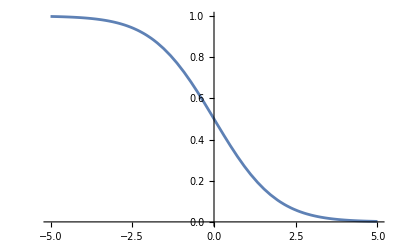

```mathematica
(3-2/(1+ⅇ^(x/(√2 ϵ))))/((1+ⅇ^(x/(√2 ϵ)))^2)
Plot[% /.ϵ->1,{x,-5,5}]
```

```mathematica
Integrate[η*D[hphi,x]*D[hpsi,x],{x,-∞,∞}]
```

ConditionalExpression[-(9 η)/(35 √2 ϵ), ]

```mathematica
Plot[hpsi /.ϵ->1,{x,-5,5}]
```

-Graphics-